### Definition

```mathematica
a=Rationalize@0.5;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=Rationalize@0.4;u0=10^-20;δstart=10^-10;m=1;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=N[- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-2/25,-1/50,-2/225,-1/200,-2/625,-1/450,-2/1225,-1/800,-2/2025,-1/1250,-2/3025,-1/1800,-2/4225,-1/2450,-2/5625,-1/3200,-2/7225,-1/4050,-2/9025,-1/5000}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
{e,SetPrecision[0.9999#[[10]],6],SetPrecision[1.0001#[[10]],6]}&[Table20REE]
```

{e,-0.00079992,-0.00080008}

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{ef,evShifted},
PrintTemporary[V];
(*Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];*)
Table[
PrintTemporary[n];
Module[{sol,evnew,steps=∞,time1,time2},
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.
FindRoot[u[e][min]==0/.sol,If[n<0,{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[evShifted],{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[Table20REE]],opt2(*,StepMonitor:>PrintTemporary[e]*)]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000799356024108875307158800370015696288485754568172) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.00252779037141606535634764484961214551074983799219) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.258100960992136653725175035849101347847353159394) is less than WorkingPrecision (TraditionalForm`50.`).

### Determine c_1

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8];
Determinec1[{start_,end___},opt___]:=Module[{aaa,findroot,mon},aaa=a;
Print[aaa];
Monitor[findroot=FindRoot[hhhc1[10^-10,c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>{mon={c1,evnhhhc1[c1]}}],mon];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{-0,-1},{MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50}]
```

1/2

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000830753307426087254373389628097812200990957538514) is less than WorkingPrecision (TraditionalForm`50.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`tan(δ) == -0.000820184896889556688039237450665701682008282575762) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

-3.0642924227327812187969946599293676148222106260674

-3.0642924227327812187969946599293676148222106260674

#### Vs_1’s eigensystem

```mathematica
AbsoluteTiming@EigenEnergy[V[r],αSch,{10^-15,Which[n<7,1000,7≤n<11,2000,11≤n<15,3000,15≤n<19,5000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->200}];
{First@%,(Last@%-Table20REE)/Table20REE}
```

$Aborted

First::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`First[$Aborted].

Last::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`Last[$Aborted].

{First[$Aborted],{-25/2 (Last[$Aborted]+2/25),-50 (Last[$Aborted]+1/50),-225/2 (Last[$Aborted]+2/225),-200 (Last[$Aborted]+1/200),-625/2 (Last[$Aborted]+2/625),-450 (Last[$Aborted]+1/450),-1225/2 (Last[$Aborted]+2/1225),-800 (Last[$Aborted]+1/800),-2025/2 (Last[$Aborted]+2/2025),-1250 (Last[$Aborted]+1/1250),-3025/2 (Last[$Aborted]+2/3025),-1800 (Last[$Aborted]+1/1800),-4225/2 (Last[$Aborted]+2/4225),-2450 (Last[$Aborted]+1/2450),-5625/2 (Last[$Aborted]+2/5625),-3200 (Last[$Aborted]+1/3200),-7225/2 (Last[$Aborted]+2/7225),-4050 (Last[$Aborted]+1/4050),-9025/2 (Last[$Aborted]+2/9025),-5000 (Last[$Aborted]+1/5000)}}

```mathematica
AbsoluteTiming[energyVs1=EigenEnergy[Vs1[r,a,c1],αSch,{10^-15,Which[n<7,1000,7≤n<11,2000,11≤n<15,3000,15≤n<19,4000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->If[n==1,1000,200]}]];
N[%,6]
```

FindRoot::brdig: The root has been bracketed as closely as possible with TraditionalForm`30.` working digits but the function value exceeds the absolute tolerance TraditionalForm`1.0000000000000009`*^-15.

General::stop: Further output of FindRoot :: brdig will be suppressed during this calculation.

{976.746,{-0.0801604,-0.0200049,-0.00888953,-0.00500015,-0.00320005,-0.00222224,-0.00163266,-0.00125,-0.000987657,-0.000800002,-0.000661158,-0.000555556,-0.000473373,-0.000408164,-0.000355556,-0.0003125,-0.000276817,-0.000246914,-0.000221607,-0.0002}}

```mathematica
N@Table20REE
```

{-0.08,-0.02,-0.00888889,-0.005,-0.0032,-0.00222222,-0.00163265,-0.00125,-0.000987654,-0.0008,-0.000661157,-0.000555556,-0.000473373,-0.000408163,-0.000355556,-0.0003125,-0.000276817,-0.000246914,-0.000221607,-0.0002}

```mathematica
(energyVs1-Table20REE)/Table20REE
```

{0.0020049803807212659052438086,0.00024290135231564454435044785,0.00007157852877338681003015222,0.00003014058469352196530461699,0.00001541871360041267995402533,8.91872423561358080679988×10^-6,5.61489015699210997964604×10^-6,3.7608590567798769224129×10^-6,2.64104552032441483890799×10^-6,1.92515252286576776031469×10^-6,1.4463014245583532849955×10^-6,1.113965283591922162217×10^-6,8.761301884105517558926×10^-7,7.0145750203468073408806×10^-7,5.7029692823385354044926×10^-7,4.6990075747351080994183×10^-7,3.9175280283550138832033×10^-7,3.3001624463988549713887×10^-7,2.8059952305778756714995×10^-7,2.4057660430814806001464×10^-7}

```mathematica
efVs1=Module[{efunction=Range@20},SetSharedVariable[efunction];
ParallelTable[efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{Which[n<11,2000,11≤n<15,3000,15≤n<19,4000,n≥19,6000],If[n<12,1.*10^-40,1.*10^-30]},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

NDSolve::precw: The precision of the differential equation (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`50.`).

General::stop: Further output of NDSolve :: precw will be suppressed during this calculation.

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\psir_a=1_efVs1.mx",efVs1];
```

#### ψ_r Vs_1

NDSolve::precw: The precision of the differential equation ({{(-0.24176315154846263548047862335291666318423795641452 Power[«2»]-2/5 Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.000221607216051951768924486796754 f[r],f[4000]==1.×10^-30,f'[4000]==-1.×10^-30},{},{},{},{}}) is less than WorkingPrecision (50.).

{1.92297×10^15                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}

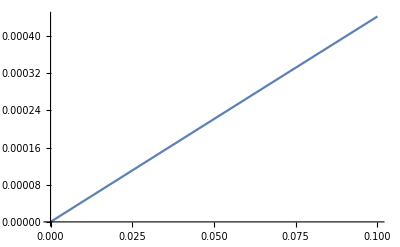

```mathematica
Module[{n=19},Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>10,4000,2000],1.*10^-30},WorkingPrecision->50,PrecisionGoal->20,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->10^-5]]
Plot[%,{r,0,0.1},AxesOrigin->{0,0}]
```

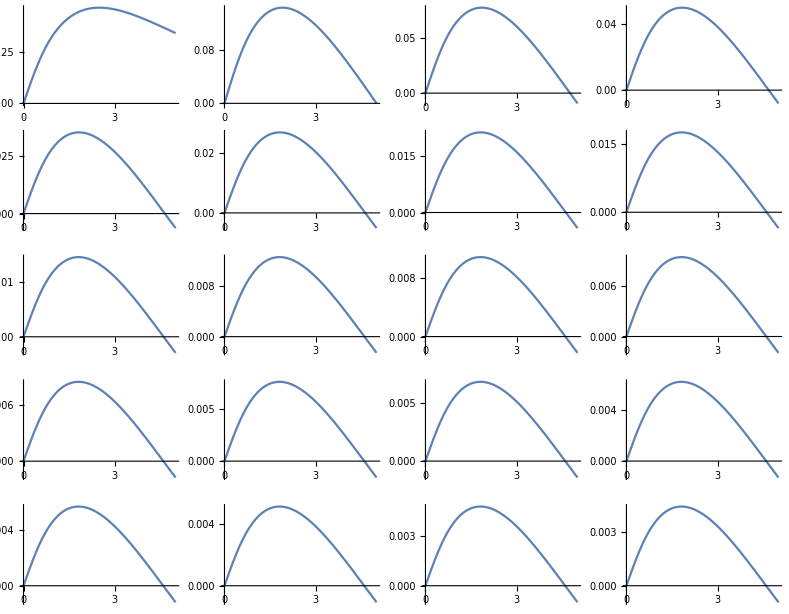

```mathematica
GraphicsGrid@Partition[Plot[efVs1[[#]],{r,0,5},ImageSize->Small,AxesOrigin->{0,0}]&/@Range@20,4]
```

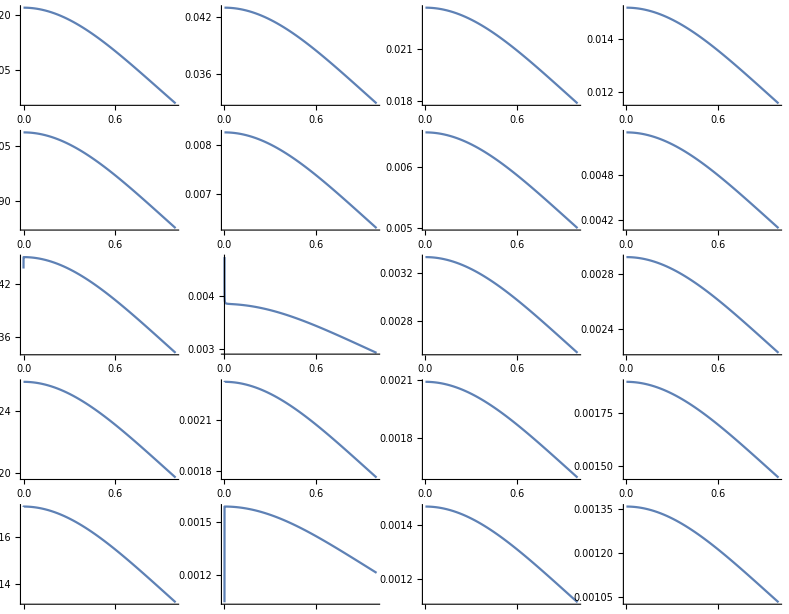

```mathematica
GraphicsGrid@Partition[Plot[efVs1[[#]]/(√(4π)r),{r,0,1},ImageSize->Small]&/@Range@20,4]
```

```mathematica
IntegrationVs11st=NIntegrate[efVs1[[#]]/(√(4π)r)δa[r] r^2,{r,0,4000},WorkingPrecision->30]&/@Range@20;
```

NIntegrate::precw: The precision of the argument function (TraditionalForm`) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`r near TraditionalForm`{r} = TraditionalForm`{0.80561348661399527470834037159424864801198122283241080984938602736655800914479412}. NIntegrate obtained TraditionalForm`0.00035254146698350104859484821176044667326063553394037923328677018549263526877908857`80. and TraditionalForm`1.8919251100805067218018517305483377429162568370609751229993843177361812113676604`80.*^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`r near TraditionalForm`{r} = TraditionalForm`{1.1283608320556826952422963305344232424585304354612409365267101429344682036454807}. NIntegrate obtained TraditionalForm`0.00029542591001832133582606994941022831074893036203448718207379167642451668945948171`80. and TraditionalForm`2.1717654339322444917159816596779497946866903093288711662097696177824124158074664`80.*^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`r near TraditionalForm`{r} = TraditionalForm`{1.1283608320556826952422963305344232424585304354612409365267101429344682036454807}. NIntegrate obtained TraditionalForm`0.00025224310611909946690057200104777329691435087218844465187309347685069871130891596`80. and TraditionalForm`6.4544265550475514352373044847622730925578173813418810074175448854496254767230135`80.*^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
ψrTrueVs1[n_][γ_]:=4π(γ IntegrationVs11st[[n]])
```

```mathematica
DetermineVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[#,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs1[#][γ]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{r0,γ}(*,N[ERROR,6]*)/.RES
]
```

```mathematica
DetermineVs1[0]
```

{0,1.42426531797632479222283514984}

Part::partw: Part TraditionalForm`3 of TraditionalForm`{207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, -0.00888888888888888937503785804087, « 15 », -0.000221606648199446233074254268555, -0.000200000000000000208918298072042}} does not exist.

NIntegrate::inumr: The integrand TraditionalForm`√2\ ⅇ^-2\ r^2\ r\ {207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, « 17 », -0.000200000000000000208918298072042}} ⟦ 3 ⟧/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

Part::partw: Part TraditionalForm`4 of TraditionalForm`{207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, -0.00888888888888888937503785804087, « 15 », -0.000221606648199446233074254268555, -0.000200000000000000208918298072042}} does not exist.

NIntegrate::inumr: The integrand TraditionalForm`√2\ ⅇ^-2\ r^2\ r\ {207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, « 17 », -0.000200000000000000208918298072042}} ⟦ 4 ⟧/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

Part::partw: Part TraditionalForm`5 of TraditionalForm`{207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, -0.00888888888888888937503785804087, « 15 », -0.000221606648199446233074254268555, -0.000200000000000000208918298072042}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand TraditionalForm`√2\ ⅇ^-2\ r^2\ r\ {207.66077, {-0.0800000000000000047355749585061, -0.0199999999999999285816615314232, « 17 », -0.000200000000000000208918298072042}} ⟦ 5 ⟧/π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries TraditionalForm`.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value TraditionalForm`{-1/250\ √2\ π + 12.5663706143591729538505735331\ NIntegrate[efVs1 ⟦ 20 ⟧\ δa(r)\ r^2/Times[« 2 »], {r, 0, 4000}, WorkingPrecision → 30]} is not a list of numbers with dimensions TraditionalForm`{1} at TraditionalForm`{γ} = TraditionalForm`{1.}.

{0,1.}

```mathematica
Module[{γη},
γlVs1={};
Monitor[Table[
γη=DetermineVs1[r0];
AppendTo[γlVs1,γη];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function (TraditionalForm`{0.00112041562865062813006366460968\ γ == 0.00159577}) is less than WorkingPrecision (TraditionalForm`30.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`{0.00112041562865062813006366460968\ γ == 0.00159513}) is less than WorkingPrecision (TraditionalForm`30.`).

FindRoot::precw: The precision of the argument function (TraditionalForm`{0.00112041562865062813006366460968\ γ == 0.00159449}) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of FindRoot :: precw will be suppressed during this calculation.

```mathematica
γrVs1=Interpolation[γlVs1]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs1[r_][n_]:=4π(γrVs1[r] IntegrationVs11st[[n]])
```

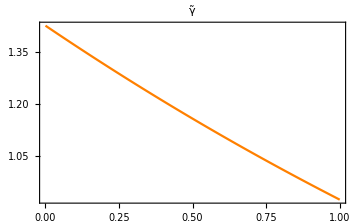

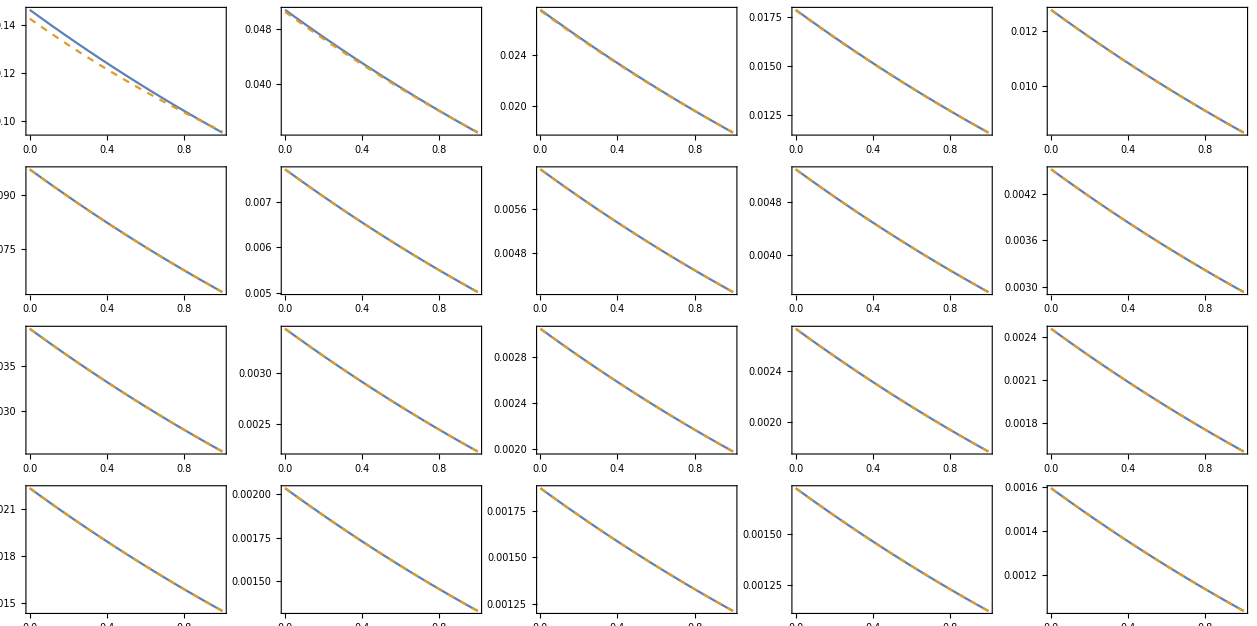

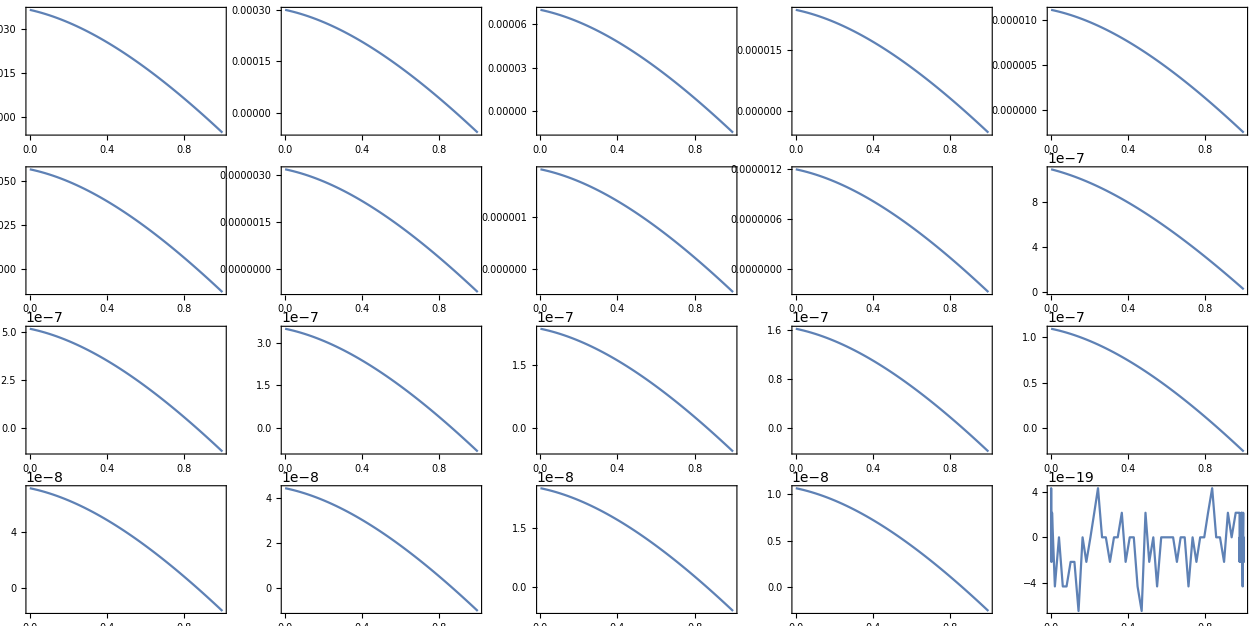

```mathematica
GraphicsGrid@{{Plot[γrVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃",Frame->True]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunVs1[r][n]-RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```

```mathematica
∇^2 Subscript[ψ, r] Subscript[Vs, 1]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
lappsi=lap[efVs1[[#]]/(√(4π)r),r]&/@Range@20
```

{1/r 6.75178×10^-307                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 1.23333×10^-130                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 5.85528×10^-71                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 1.63347×10^-40                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 7.55818×10^-22                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 3.89828×10^-9                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 7.15336                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 8.42079×10^7                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 3.18698×10^13                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 1.02316×10^18                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 2000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 9.56691×10^7                                                                              -41
InterpolatingFunction[{{9.999999999999999292928793998801450023306451190620 10   , 3000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 440.756                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 3.70988×10^6                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 8.62255×10^9                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 3000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 2120.14                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 5.49366×10^6                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 5.53223×10^9                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 2.47071×10^12                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 4000.0000000000000000000000000000000000000000000000}}, <>](r),1/r 1.58039                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 6000.0000000000000000000000000000000000000000000000}}, <>](r),-1/r 2761.63                                                                              -31
InterpolatingFunction[{{9.999999999999999081741125669838514854651381156291 10   , 6000.0000000000000000000000000000000000000000000000}}, <>](r)}

```mathematica
ψrTruelap[n_][γ_]:=4π(γ IntegrationVs11st[[n]])
```

```mathematica
DeterminelapVs1[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[RS[#,r]/(√(4π)),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ]&/@REFRANGE==REF],{γ,0,1},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ}}/.RES
]
```

```mathematica
DeterminelapVs1[0.1]
```

FindRoot::precw: The precision of the argument function (TraditionalForm`{0.00112041562865062813006366460968\ γ == -0.0122617}) is less than WorkingPrecision (TraditionalForm`30.`).

(0.1 | -10.9438543320558472039055050844)

```mathematica
Quiet@Module[{max=1,interval=0.001},
(*Zl=Determine[0][[1]];*)γllapVs1={};(*ηl={};*)
Monitor[Table[Module[{γη},
γη=DeterminelapVs1[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllapVs1,γη[[1]]];
(*AppendTo[ηl,γη[[2]]];*)]
,{r0,0.001,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
γrlapVs1=Interpolation[γllapVs1]
```

InterpolatingFunction[{{0.001, 1.}}, <>]

```mathematica
ψrfunlapVs1[r_][n_]:=4π(γrlapVs1[r] IntegrationVs11st[[n]])
```

```mathematica
lapRS[r_]=lap[RS[n,r]/(√(4π)),r]
```

(8 √(2/(5 π)) ⅇ^(-(2 r)/(5 n)) (3 (r-5 n) 1-n2(4 r)/(5 n)-(n-1) (3 (5 n-2 r) 2-n3(4 r)/(5 n)-2 (n-2) r 3-n4(4 r)/(5 n))))/(375 n^(7/2) r)

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

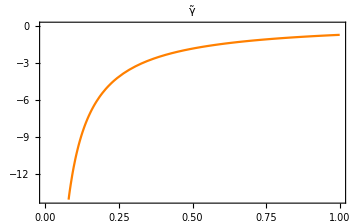

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

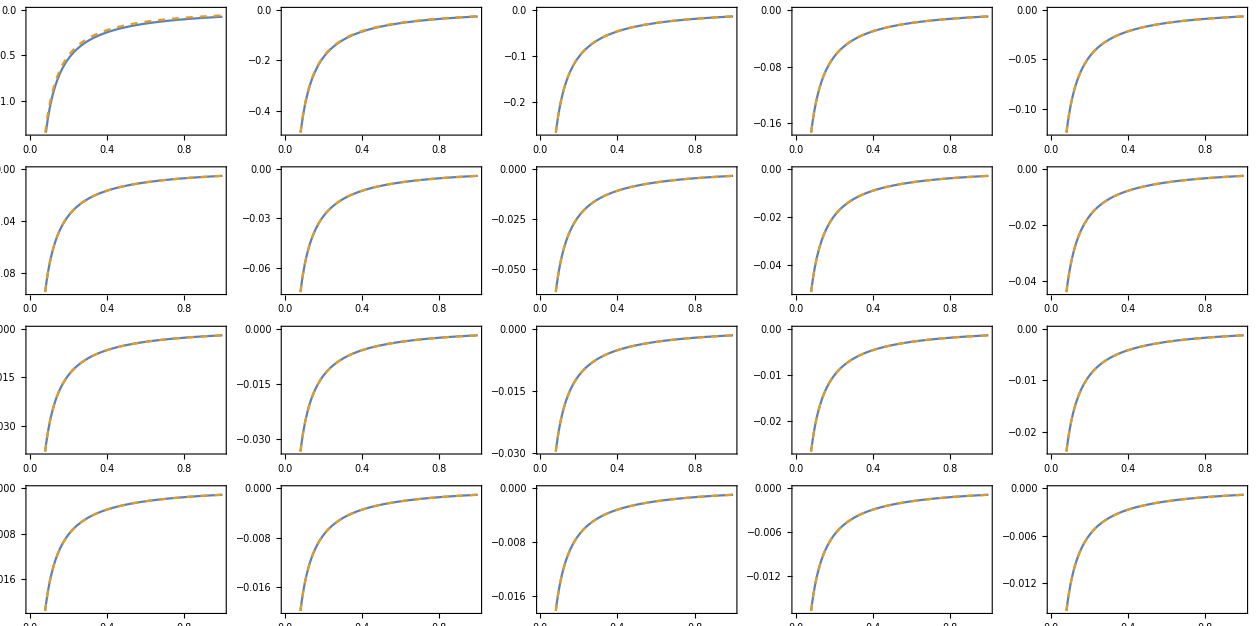

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

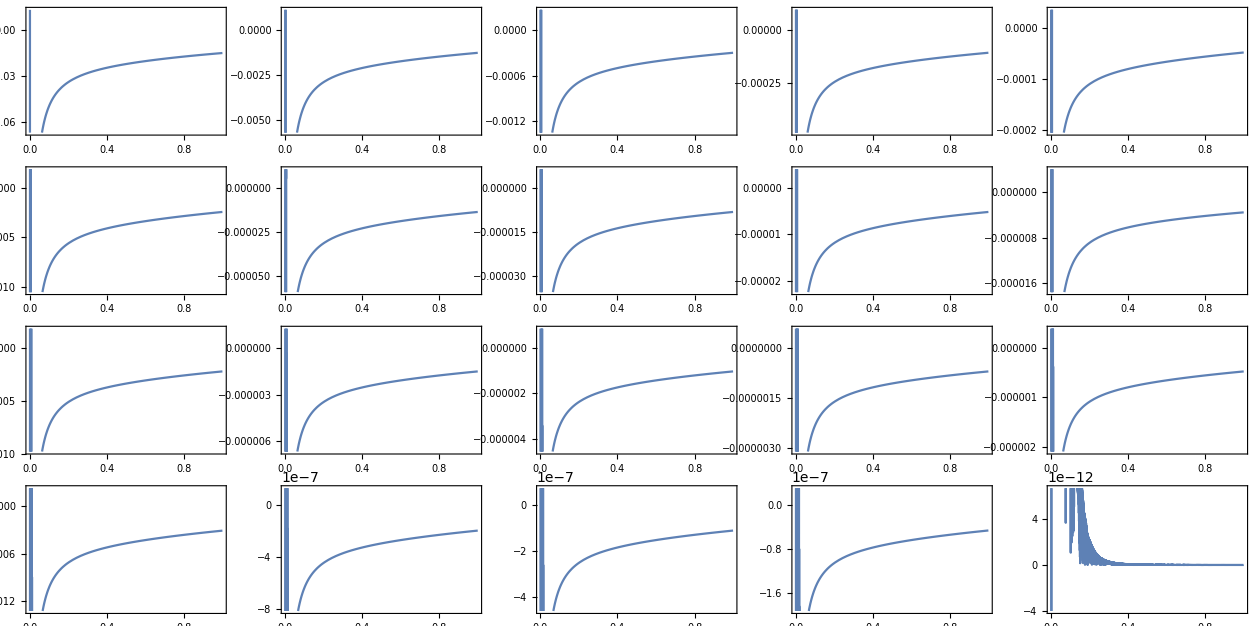

```mathematica
GraphicsGrid@{{Plot[γrlapVs1[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃",Frame->True]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs1[r][n],lapRS[r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
GraphicsGrid@Partition[Table[Plot[{ψrfunlapVs1[r][n]-lapRS[r]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230,Frame->True,Axes->False],{n,1,20}],5]
```

### Determine c_2 & d_1

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus5,8];
```

```mathematica
Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus5},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2}}],mon];
{c2,d1}/.findroot
]
```

```mathematica
Remove[c2,d1,hhh,evnhhh1,evnhhh2]
```

```mathematica
{c2,d1}=Determinec2d1[{-6},{0.5}]
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00071619821791746368773586873382713613327837949716) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.23039435424540094800222171113130004245254631422) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.380962 Power[«2»]-0.5 Plus[«2»]+1. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00071619821791746368773586873382713613327837949716) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion_c2d1.mx",{c2,d1}];
```

```mathematica
ContourPlot[{hhh[ee[[1]],c2,d1]-δexpminus10,hhh[ee[[2]],c2,d1]-δexpminus5},{c2,10,-10},{d1,-10,10},PlotPoints->100]
```

#### Vs_2’s eigensystem

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,6000,n≥19,8000]},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001249,-0.001251},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[20]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001385,-0.0013851},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[19]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001543,-0.0015433},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[18]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001730,-0.001731},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[17]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.001953,-0.0019532},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[16]]=%
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,4000},{-0.0022221,-0.0022223},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
energyVs2[[15]]=%
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Coulomb_psir_comparasion_energyVs2.mx",energyVs2];
```

```mathematica
(energyVs2-Table20REE)/Table20REE
```

```mathematica
efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];*)
(*REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=Limit[RS[n,r]/(√(4π)),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrue[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];*)
(*Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
DetermineVs2[0]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=Determine[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[1]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γr[r] Integration1st[[n]]+ηr[r] a^2 Integration2nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],RS[n,r]/(√(4π))},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```